## 5.1

```mathematica
a[β_,s0_,starting_]:=Module[{γ,i0,soln,i,s},
γ=0.4;
i0=1;
soln=NDSolve[{
s'[t]==-β s[t] i[t],s[0]==s0,
i'[t]==β s[t] i[t]-γ i[t], i[0]==i0},{s,i},{t,0,100}];
s[t_]=s[t]/.soln;
i[t_]=i[t]/.soln;
{
Plot[{s[t],i[t],s0-(s[t]+i[t])},{t,0,20},GridLines->Automatic,PlotLegends->{"Susceptable","Infected","Recovered"}], (*Plot from 0 to 20*)
"Never Infected"->s[100], (*People never infected*)
"Max Infected" ->i[t]/.FindRoot[i'[t],{t,starting}] (*Max infected*)
}//MatrixForm
]
```

### a.

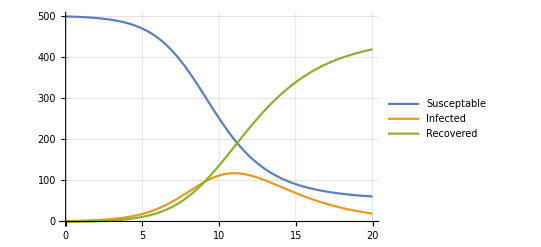
(-Graphics-
Never Infected→{53.3125}
Max Infected→{117.742})

```mathematica
a[.002,500,11]
```

### b.

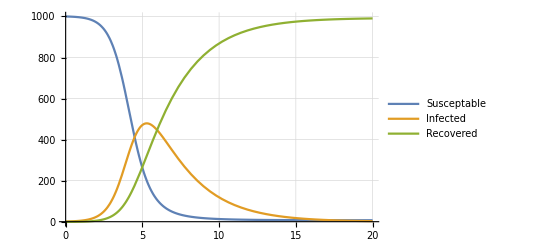
(-Graphics-
Never Infected→{6.9411}
Max Infected→{479.112})

```mathematica
a[.002,1000,6]
```

### c.

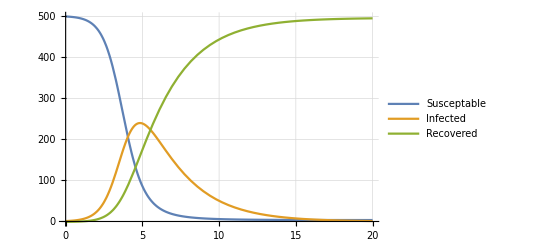
(-Graphics-
Never Infected→{3.45262}
Max Infected→{240.056})

```mathematica
a[0.004,500,5]
```